```mathematica
(*Ako ˇzelite da ogradite parcelu u obliku pravougaonika dimenzija 200m×60m,a znamo
da je greˇska prilikom merenja ne ve ́ca od 3cm,na ́ci pribliˇznu vrednost povrˇsine ove parcele
i granicu apsolutne i relativne greˇske.*)
```

```mathematica
p=200*60
```

12000

```mathematica
pmax=200.03*60.03
```

12007.8

```mathematica
pmin=199.07*59.07
```

11759.1

```mathematica
ag=Abs[Max[pmax-p,pmin-p]]
```

7.8009

```mathematica
rg=ag/Abs[p]
```

0.000650075

```mathematica
cv={{8,132},{11,137},{13,142},{16,153},{22,148}}
```

{{8,132},{11,137},{13,142},{16,153},{22,148}}

```mathematica
(*Na ́ci Lagranˇzov oblik interpolacionog polinoma,koji interpolira ove podatke.*)
```

```mathematica
lagranz[cv_,x_]:=Module[{},
m=Length[cv];
w=1;
pol=0;
Do[
w=w*(x-cv[[i,1]]),
{i,1,m}];
Do[
wi=w/(x-cv[[i,1]]);
pol=pol+cv[[i,2]]*wi/(wi/.x->cv[[i,1]]),
{i,1,m}];
pol
]
```

```mathematica
lag[x_]=lagranz[cv,x]//N
```

0.0785714 (-22.+x) (-16.+x) (-13.+x) (-11.+x)-0.415152 (-22.+x) (-16.+x) (-13.+x) (-8.+x)+0.525926 (-22.+x) (-16.+x) (-11.+x) (-8.+x)-0.2125 (-22.+x) (-13.+x) (-11.+x) (-8.+x)+0.017797 (-16.+x) (-13.+x) (-11.+x) (-8.+x)

```mathematica
kubnisplajn=Interpolation[cv,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
tac=151
```

151

```mathematica
(*lag*)
```

```mathematica
apx=lag[15]
```

149.1

```mathematica
ag=Abs[apx-tac]
```

1.9

```mathematica
rg=ag/tac
```

0.0125828

```mathematica
(*spl*)
```

```mathematica
apxs=kubnisplajn[15]//N
```

148.8

```mathematica
ags=Abs[apxs-tac]
```

2.2

```mathematica
rgs=ags/tac
```

0.0145695

```mathematica
(*Na ́ci linearnu funkciju,koja najbolje aproksimira ove podatke (u smislu najmanjih kvadrata)
i na jednom grafiku nacrtati date podatke i dobijenu funkciju.*)
```

```mathematica
cv={{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}
```

{{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}

```mathematica
najkva=Fit[cv,{1,t},t]
```

23.084-0.00661922 t

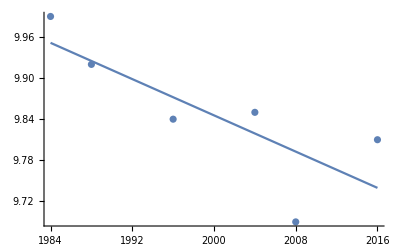

```mathematica
Show[ListPlot[cv],Plot[najkva,{t,1984,2016}],PlotRange->All]
```

```mathematica
(*Napisati program koji za zadati skup od n+1 ˇcvorova kreira interpolacioni polinom
n-tog stepena u obliku p(x)=a0+a1(x−1000)+a2(x−1000)2+ . . .+an(x−1000)n i testirati ga na problemu iz tre ́ceg zadatka.*)
```

```mathematica
cv={{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}
```

{{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}

```mathematica
zad4[cv_,x_]:=Module[{},
m=Length[cv];
a=Table[1,{i,1,m},{j,1,m}];
b=Table[cv[[i,2]],{i,1,m}];
Do[
a[[i,j]]=(cv[[i,1]]-1000)^(j-1),
{i,1,m},{j,2,m}];
koef=LinearSolve[a,b];
baza=Table[(x-1000)^i,{i,0,m-1}];
koef.baza
]
```

```mathematica
p=zad4[cv,x]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,984.,968256.,9.52764×10^8,9.3752×10^11,9.22519×10^14},{1.,988.,976144.,9.6443×10^8,9.52857×10^11,9.41423×10^14},{1.,996.,992016.,9.88048×10^8,9.84096×10^11,9.80159×10^14},{1.,1004.,1.00802×10^6,1.01205×10^9,1.0161×10^12,1.02016×10^15},{1.,1008.,1.01606×10^6,1.02419×10^9,1.03239×10^12,1.04065×10^15},{1.,1016.,1.03226×10^6,1.04877×10^9,1.06555×10^12,1.0826×10^15}} may contain significant numerical errors.

-9.42748×10^8+4.72459×10^6 (-1000+x)-9470.59 (-1000+x)^2+9.49171 (-1000+x)^3-0.00475628 (-1000+x)^4+9.53311×10^-7 (-1000+x)^5